# Sheeyat for the Boundary Paper

```mathematica
AppendTo[$Path,"/Users/michelbuck/Dropbox/mathematica/causet/"];
Needs["Causet`"];
blue=RGBColor[66/255,106/255,181/255];
yellow=RGBColor[255/255,204/255,17/255];
red=RGBColor[255/255,99/255,71/255];
grey=RGBColor[135/225,128/225,118/225];
```

```mathematica
(*rasterOption=Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}*)
```

```mathematica
Complement[Options@ListPlot,Options@Graphics]
```

{AspectRatio→1/GoldenRatio,Axes→True,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,DataRange→Automatic,Filling→None,FillingStyle→Automatic,InterpolationOrder→None,Joined→False,MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotStyle→Automatic,TargetUnits→Automatic,PerformanceGoal:>$PerformanceGoal}

```mathematica
Options
```

```mathematica
$UserBaseDirectory
```

/Users/mb909/Library/Mathematica

## Plot of N_(min/max):

```mathematica
f=.5+.25Sin[.5#]*Sin[1.5#]&;
```

```mathematica
plot[n_]:=
Module[{s, above, below, region,x , t},
s=CSMinkowski2Rectangle[5.,1.,n];
below=Or[t<f[x]&&t-#[[2]]>Abs[x-#[[1]]]]&/@CPoints[s][[MaximalBelowSurface[s,f]]];
Print[below];
above=Or[t>f[x]&&-(t-#[[2]])>Abs[x-#[[1]]]]&/@CPoints[s][[MinimalAboveSurface[s,f]]];
Print["above = ",above];
region={below,above};
{Show[
CPlot[s,Highlight->Join[MaximalBelowSurface[s,f],MinimalAboveSurface[s,f]],HighlightStyle->{Black,PointSize[0.008]},PlotStyle->{Black,PointSize[0.008]},ShowLinks->True,Frame->False,AspectRatio->1/5],  
Plot[f[x],{x,0,5},PlotStyle->Directive[Thick,Black]],
RegionPlot[region,{x,0,5},{t,0,1},MaxRecursion->10,BoundaryStyle->Black,Mesh->None ,PlotStyle->Directive[blue,Opacity[0.05]]],
Graphics[{White}~Join~{Disk[#,0.012]&/@CPoints[s][[Join[MaximalBelowSurface[s,f],MinimalAboveSurface[s,f]]]]}],ImageSize->800],
RegionPlot[region,{x,0,5},{t,0,1},MaxRecursion->9,BoundaryStyle->Black,Mesh->None ,PlotStyle->Directive[blue,Opacity[0.05]]]}
]
```

```mathematica
p=plot[10]
```

{t$8038<0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&-0.227286+t$8038>Abs[-1.74867+x$8038],t$8038<0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&-0.441201+t$8038>Abs[-4.21521+x$8038]}

above = {t$8038>0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&0.479556-t$8038>Abs[-3.60433+x$8038],t$8038>0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&0.640848-t$8038>Abs[-4.21337+x$8038],t$8038>0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&0.683677-t$8038>Abs[-0.613599+x$8038],t$8038>0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&0.714823-t$8038>Abs[-2.01797+x$8038],t$8038>0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&0.779484-t$8038>Abs[-2.79238+x$8038],t$8038>0.5+0.25 Sin[0.5 x$8038] Sin[1.5 x$8038]&&0.996103-t$8038>Abs[-2.52772+x$8038]}

{-Graphics-,-Graphics-}

```mathematica
plot[n_]:=Module[{s, above, below, region,x , t},
s=CSMinkowski2Rectangle[5.,1.,n];
below=Or[t<f[x]&&t-#[[2]]>Abs[x-#[[1]]]]&/@CPoints[s][[MaximalBelowSurface[s,f]]];
above=Or[t>f[x]&&-(t-#[[2]])>Abs[x-#[[1]]]]&/@CPoints[s][[MinimalAboveSurface[s,f]]];
region={below,above};

Show[CPlot[s,Highlight->Join[MaximalBelowSurface[s,f],MinimalAboveSurface[s,f]],PlotStyle->PointSize[0.008],ShowLinks->True,Frame->False,AspectRatio->1/5],Plot[f[x],{x,0,5},PlotStyle->Directive[Thick,Black]],RegionPlot[region,{x,0,5},{t,0,1},MaxRecursion->9,BoundaryStyle->Black,Mesh->None,PlotStyle->Directive[blue,Opacity[0.05]]],ImageSize->800]
]
```

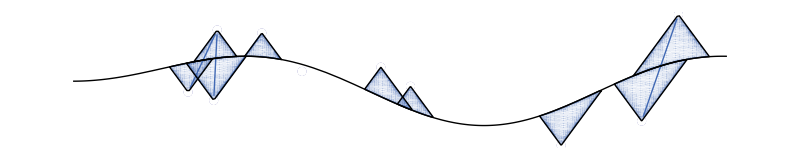

```mathematica
plot[10]
```

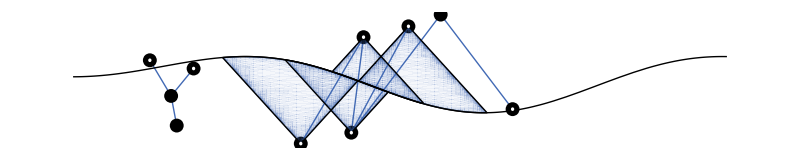
rasterTrick[-Graphics-]

```mathematica
rasterTrick@p
```

```mathematica
Export["mylatestplot.pdf",-Graphics-,"AllowRasterization"->True,ImageSize->600,ImageResolution->300]
```

mylatestplot.pdf

```mathematica
rasterTrick@
```

```mathematica
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

Export["region.pdf",-Graphics-//rasterTrick]
```

region.pdf

## Changing CPlot function - NOT INTERESTING

```mathematica
sprinkling=CSMinkowski2Diamond[100];
```

```mathematica
(* Here are default options for CPlot. They can be overwritten in CPlot[]. The pattern is described in http://bit.ly/1hPag7u *)
Options[CPlot] = {Frame ->  True, ShowLinks -> False, ShowLabels -> False, Highlight -> None}~Join~Options@ListPlot~Join~Options@ListPointPlot3D;

(* Use SyntaxInformation to make sure that custom options in CPlot are correctly highlighted *)
SyntaxInformation[CPlot] = {"ArgumentsPattern" -> {__, OptionsPattern[]}};

(* The parameter ϵ determines the fraction by which the plot range exceeds the range of sprinkled points. *)
CPlot[sprinkling_List, opts:OptionsPattern[{ListPlot, ListPointPlot3D, CPlot}]] :=
Module[{plot, points = CEmbedding@sprinkling, size = CSize@sprinkling, dim = CDim@sprinkling, ϵ = 0.05, max, min, rangerule, stylerule, pointsize, display},
pointsize = Which[size >= 300 && dim == 3, 0.01, size >= 500 && dim == 2, 0.0075, True, 0.0125];
max = Max /@ Transpose@points;
min = Min /@ Transpose@points;
rangerule = PlotRange -> Transpose@{min - 1 * pointsize , max + 1 * pointsize};
stylerule = PlotStyle -> Directive[If[OptionValue[ShowLinks], Black, blue], PointSize[pointsize]];
Which[
dim == 2, 
    plot = ListPlot[points, Evaluate@FilterRules[{opts, PlotRange -> All, stylerule, Axes -> None, Frame -> True, AspectRatio->#[[2]]/#[[1]]&@(max-min)}, Options@ListPlot]];
	display = {plot};
	If[OptionValue[ShowLabels], AppendTo[display, Graphics[Text[#[[1]], #[[2]] - 0.015 * (max-min)]& /@ Transpose@{Range@CSize@sprinkling, CEmbedding@sprinkling}]]];
    If[OptionValue[ShowLinks], AppendTo[display, Graphics[{blue, Sequence@@LinkLines@sprinkling}]]]
	(*Show[Graphics[Point[{blue, Sequence@@LinkLines@sprinkling}]]]*),
dim == 3, 
    plot = ListPointPlot3D[points, Evaluate@FilterRules[{opts, rangerule, stylerule, BoxRatios -> max - min}, Options@ListPointPlot3D]];
	display = {plot};
	If[OptionValue[ShowLabels], AppendTo[display, Graphics3D[Text[#[[1]], #[[2]] - 0.015 * (max-min)]& /@ Transpose@{Range@CSize@sprinkling, CEmbedding@sprinkling}]]];  
	If[OptionValue[ShowLinks], AppendTo[display, Graphics3D[{blue, Sequence@@LinkLines@sprinkling}]]]
];
If[!OptionValue[Highlight]===None,AppendTo[display,Graphics[{PointSize[pointsize],Point/@points[[{Sequence@@OptionValue@Highlight}]]}]]];
Show[display]
];
```

```mathematica
CPlot[s,Highlight->InRegion[s,(#[[1]])^2+(#[[3]])^2<0.2&],ShowLabels->False,HighlightStyle->{blue,PointSize[0.5]}]
```

-Graphics3D-

```mathematica
{1,Sequence@@2,3}
```

{1,2,3}

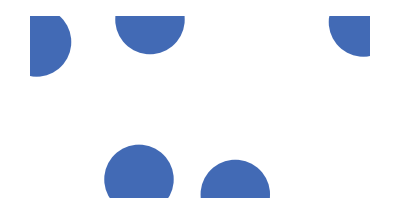

```mathematica
Graphics[{PointSize[0.2],RGBColor[22/85,106/255,181/255],{Point[{0.18249757721084,0.2334894257854144}],Point[{-0.09653925228675067,0.2773257076808261}],Point[{-0.39331776878696534,0.6764412193914799}],Point[{0.5538075992443112,0.7344822274077738}],Point[{-0.06467365217842641,0.7416449812010595}]}}]
```

```mathematica
l={1,2,3}
```

{1,2,3}

```mathematica
{a,Sequence[l,Depth@l-1],c}
```

{a,{1,2,3},1,c}

```mathematica
Depth[{1}]
```

2

```mathematica
{Sequence[RGBColor[1,2,3],Depth@}}
```

{{1,2,3}}

```mathematica
Set[1]
```

Set::setraw: Cannot assign to raw object 1.

Sequence[]

```mathematica
s=CSMinkowski3Diamond[1000];
```

```mathematica
Options[myFunction] = {myOption ->None};
```

```mathematica
ListQ@RGBColor[0,1,2]
```

False

```mathematica
myFunction[opts:OptionsPattern[myFunction]]:=Module[{highlightoptions},
highlightoptions=If[ListQ@OptionValue[myOption]==1,{OptionValue[myOption]},OptionValue[myOption]]
If[!OptionValue[myOption]===None,
OptionValue@myOption,
Print["No Option Specified"]
]
]
```

```mathematica
myFunction[myOption->{blue}]
```

{RGBColor[22/85,106/255,181/255]}

```mathematica
Sequence@@Flatten@{a,{RGBColor[1,2,3],c}}
```

Sequence[a,RGBColor[1,2,3],c]

```mathematica
{a,Sequence@RGBColor[1,2,3],c}
```

{a,RGBColor[1,2,3],c}

```mathematica
s=
```

```mathematica
s=CSMinkowski3Diamond[20]
```

{{{0.277293,1.99098,-0.366314},{0.553531,4.68094,-0.318822},{0.460074,5.42829,-0.286248},{0.713015,5.82071,-0.251306},{0.686794,6.20325,-0.227597},{0.118049,2.34002,-0.209391},{0.657706,3.5314,-0.17534},{0.419219,1.44299,-0.166289},{0.797179,4.48111,-0.0615991},{0.528237,1.56289,-0.0151666},{0.910867,0.57091,0.0561492},{0.398411,1.13603,0.0651789},{0.0454749,3.05619,0.0864245},{0.609603,1.36352,0.109918},{0.386332,3.05569,0.233553},{0.585587,4.00929,0.255966},{0.513843,5.71154,0.37134},{0.494175,4.23283,0.37224},{0.0436331,1.24363,0.422048},{0.493545,3.09269,0.440635}},CSMinkowski3Diamond,3,20,0.523599,1.}

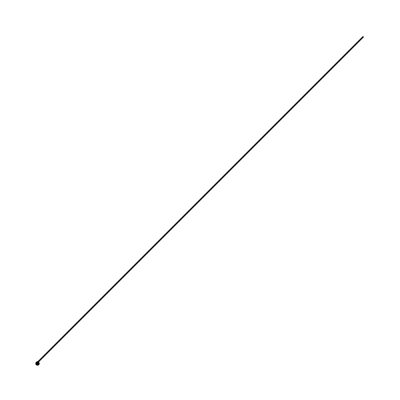

```mathematica
Show[Graphics[Line[{{0,0},{1,1}}]],Graphics[Point[{0,0}]]]
```

```mathematica
CPlot[s,Highlight->{1,2,3},ShowLinks->True,HighlightStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
{#}&/@1
```

1

```mathematica
Point/@points[[{1,2}]]
```

{Point[{0.489528,0.494039}],Point[{0.630286,0.636222}]}

```mathematica
{Sequence@@1}
```

{1}

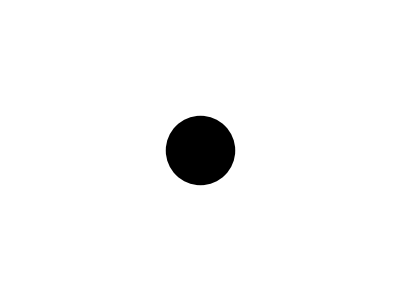

```mathematica
Graphics[{PointSize[10],Point[{0,0}]}]
```

```mathematica
Show@Graphics[{Blue,Point/@points[[{Sequence@@{1,3,4,5,6,7}}]]}]
```

-Graphics-

## The coordinate plot:

```mathematica
top={0,0,0};hcone=0.7;rcone=hcone;a=1;b=5;c=2;d=5;
```

```mathematica
updatePlots[a_,b_,c_,d_]:=Module[{},
surface[x_,y_]:=(a x^2+b y^2-c x y)/d;

rintersect[θ_]:=hcone(-1+ √(1+4 surface[Cos[θ],Sin[θ]] rcone^2/hcone))/(2 surface[Cos[θ],Sin[θ]] rcone);

conePlot=ParametricPlot3D[{rcone(1-z/hcone)Cos[θ],rcone(1-z/hcone)Sin[θ],z},{z,0,hcone},{θ,0,2π},Mesh->None,PlotStyle->Directive[Opacity[0.5],blue],PlotRange->{{-1,1},{-1,1},{0,1.4hcone}},BoxRatios->{2,2,1.4hcone},RegionFunction->Function[{x,y,z},z>surface[x,y]],Ticks->None(*{None,None,{{hcone,Style["T",FontSize->18,FontFamily->"Helvetica",Italic]}}}*)];

intersectionPlot=ParametricPlot3D[{rintersect[θ]Cos[θ],rintersect[θ]Sin[θ],rintersect[θ]^2 surface[Cos[θ],Sin[θ]]},{θ,0,2π},PlotStyle->Black];

intersectionPlotProjected=ParametricPlot3D[{rintersect[θ]Cos[θ],rintersect[θ]Sin[θ],0},{θ,0,2π},PlotStyle->Directive[Black,Thick]];

intersectionPlotBars=ListPointPlot3D[Table[{rintersect[θ]Cos[θ],rintersect[θ]Sin[θ],rintersect[θ]^2 surface[Cos[θ],Sin[θ]]z},{θ,0,2π,2π/100},{z,0,1,0.1}],PlotStyle->Directive[Black,PointSize[0.001],Opacity[1]]];

surfacePlot=Plot3D[surface[x,y],{x,-1,1},{y,-1,1},PlotStyle->Directive[White,Opacity[0.5],Specularity[White,20]],Mesh->20,MeshStyle->Opacity[0.5],BoundaryStyle->None,PlotRange->Full] ;

arrowPlot=Graphics3D[{Arrowheads[{0.02}],Thickness[0.003],Arrow[{{0,0,0},{rintersect[θ0]Cos[θ0],rintersect[θ0]Sin[θ0],0}/.{θ0-> 40Degree}}],
Arrow[{{0,0,0},{0,0,hcone}}]}];
]
textPlot=Graphics3D[{Text[Style["r_max(ϕ)",FontSize->18,FontFamily->"Helvetica",Italic,Opacity[1.0]],0.75{Cos[θ0],Sin[θ0],0}/.{θ0-> 40Degree}],Text[Style["T",FontSize->18,FontFamily->"Helvetica",Italic,Opacity[1.0]],{-0.04,0.06,hcone}]}];
```

```mathematica
updatePlots[5,5,0,18]
Show[conePlot,surfacePlot,intersectionPlot,intersectionPlotBars,intersectionPlotProjected,arrowPlot,textPlot,Boxed->False,AxesOrigin->{0,0,0},Lighting->"Neutral"]
```

-Graphics3D-